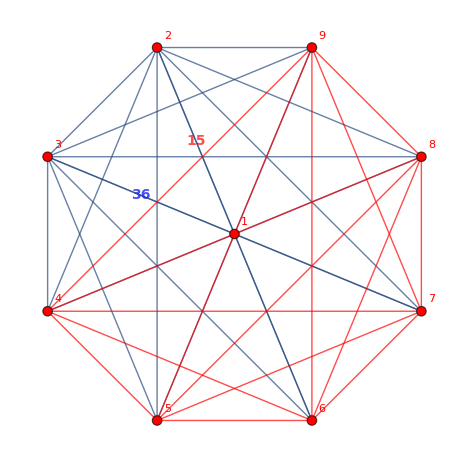
```mathematica
Table[ChromaticPolynomial[-Graphics-,k],{k,0,10}]
```

{0,0,0,0,0,0,0,0,0,362880,3628800}

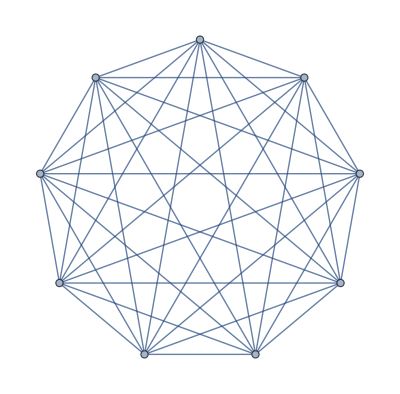

```mathematica
g=CompleteGraph[9]
```

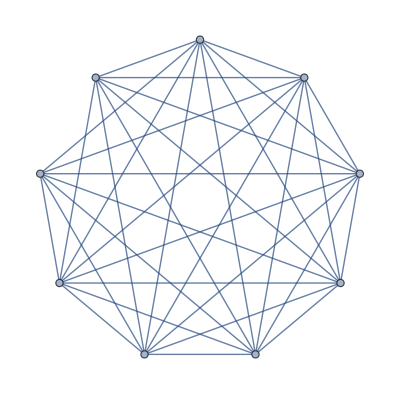
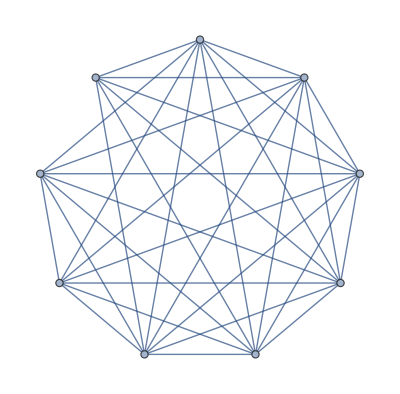
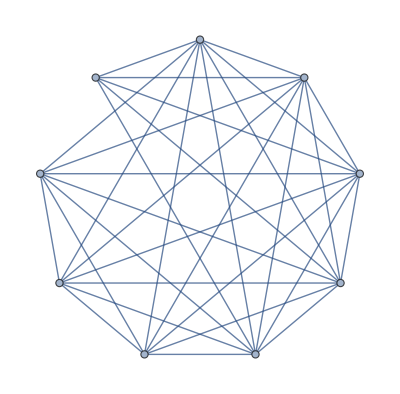
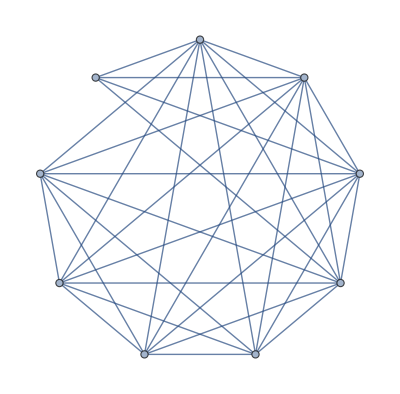
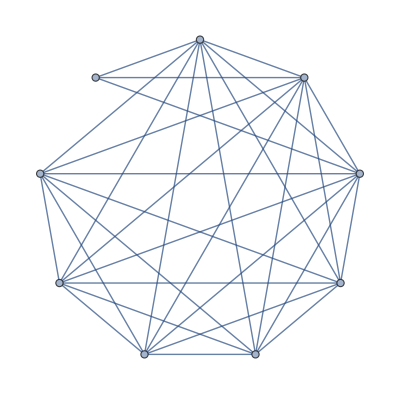
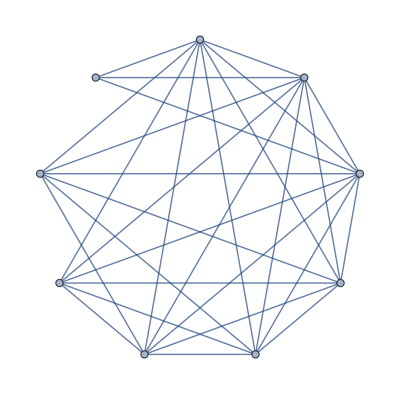
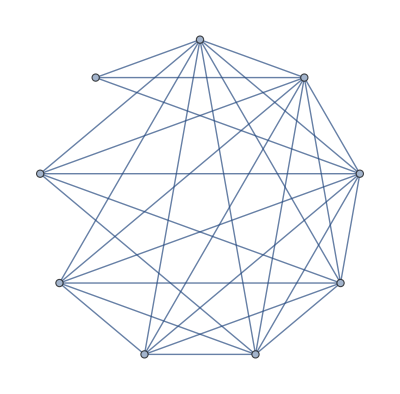
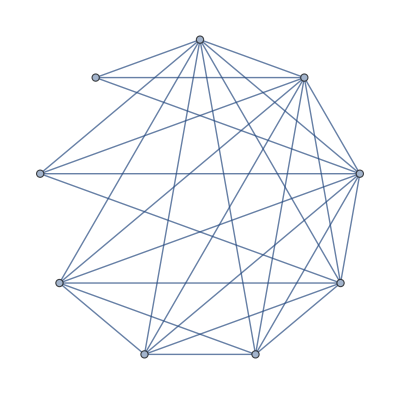

```mathematica
Table[g=EdgeDelete[g,e],{e,EdgeList[CompleteGraph[6]]}]
```

```mathematica
Table[ChromaticPolynomial[g,k]/24,{k,0,10}]
```

{0,0,0,0,1,160,3645,35840,218750,979776,3529470}

```mathematica
160-24
```

136

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[g,x]]
```

{0,0,0,0,1,31,90,65,15,1}

```mathematica
160/5
```

32

```mathematica
((3645/5)-31-1)/6
```

697/6